## Get helper functions

```mathematica
NotebookEvaluate[FileNameJoin[{NotebookDirectory[],"UTILITY_readBeamFiles.nb"}]]
```

## Import

```mathematica
fileName= FileNameJoin[{NotebookDirectory[],"beams/optimizerRunningBestBeam_PENT.h5"}];
(*fileName= FileNameJoin[{NotebookDirectory[],"demo.h5"}];*)


data = readBeamFile[fileName];
(*{driverData,witnessData} = getDriverAndWitness[data];*)
```

### Optional: Remove outliers

```mathematica
Length[data]
```

9997

```mathematica
data = DeleteAnomalies[data];
```

```mathematica
Length[data]
```

9831

## Visualize

```mathematica
densityHistogramMod[10^6{#x,#px/#pz}&/@data,{100,100},LabelStyle->20,ImageSize->400]
densityHistogramMod[10^6{#x,#y}&/@data,{100,100},LabelStyle->20,ImageSize->400]
(*densityHistogramMod[{#x,#px/#pz}&/@driverData,{100,100}(*,LabelStyle->20,ImageSize->800*)]
densityHistogramMod[{#x,#px/#pz}&/@witnessData,{100,100}(*,LabelStyle->20,ImageSize->800*)]*)
```

-Graphics-

-Graphics-

```mathematica
densityHistogramMod[{10^6#z,10^-9#pz}&/@data,{100,100},LabelStyle->20,ImageSize->400]
```

-Graphics-

```mathematica
densityHistogramMod[{10^-9#pz,10^6#x}&/@data,{100,100},LabelStyle->20,ImageSize->400]
densityHistogramMod[{10^-9#pz,10^6#px/#pz}&/@data,{100,100},LabelStyle->20,ImageSize->400]
```

-Graphics-

-Graphics-

5.4586

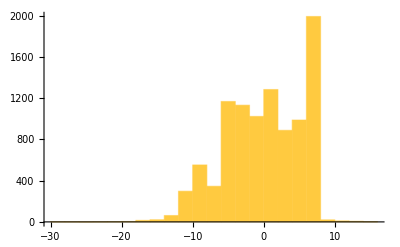

```mathematica
StandardDeviation[10^6 data[[All,"z"]]]
Histogram[10^6 data[[All,"z"]]]
```

```mathematica
img3D = ListPointPlot3D[
{10^3#x,10^-9#pz,10^3#px/#pz}&/@data,
(*DeleteAnomalies[
{10^3#x,10^-9#pz,10^3#px/#pz}&/@data,
Method->"Multinormal"(*"KernelDensityEstimation" is the default but "Multinormal" seems more than adequate*)
],*)
SphericalRegion->True,
ImageSize->800,
(*ColorFunction->"Rainbow",*)
ColorFunction->(ColorData["Rainbow"][#2]&),
BoxRatios->{1,1,1},
PlotRange->All,
AxesLabel->{"x [mm]","pz [GeV]","x' [mrad]"},
LabelStyle->20,
AxesStyle->{ColorData[97][1],ColorData[97][2],ColorData[97][3]}
]
```

-Graphics3D-

#### Animation

```mathematica
(*
img3D = ListPointPlot3D[{#x,#px/#pz,#pz}&/@data,ImageSize->800,ColorFunction->"Rainbow",BoxRatios->{1,1,1},PlotRange->All,LabelStyle->20,Ticks->None]

tourSteps =Table[
Scaled[{2*Cos[ϕ],2*Sin[ϕ],0}],
{ϕ,0,2π,π/32}
];

Parallelize[Tour3DVideo[img3D,tourSteps]]*)
```

```mathematica
(*imgArr=ParallelTable[
Rasterize[
ListPointPlot3D[
{10^3#x,10^3#px/#pz,10^-9#pz}&/@data,
SphericalRegion->True,
ImageSize->800,
ColorFunction->"Rainbow",
BoxRatios->{1,1,1},
PlotRange->All,
AxesLabel->{"x [mm]","pz [GeV]","x' [mrad]"},
LabelStyle->20,
AxesStyle->{ColorData[97][1],ColorData[97][2],ColorData[97][3]},
ViewPoint->{Cos[ϕ],0.75,Sin[ϕ]},
ViewVertical->{0,1,0}
],
RasterSize->800
],
{ϕ,0,2π,π/32}
];

Export["~/anim.gif",imgArr]*)
```

#### Alternate animation

```mathematica
(*
tourVid = Parallelize[Tour3DVideo[img3D]]

Export[
"~/x_xp_pz.gif",
VideoFrameList[tourVid,100]
]*)
```

## Linear propagation

```mathematica
ClearAll[z]
```

```mathematica
Plot[
Evaluate[10^6{
StandardDeviation[
(#x + z*#px/#pz)&/@driverData
],
StandardDeviation[
(#x + z*#px/#pz)&/@witnessData
],
StandardDeviation[
(#y + z*#py/#pz)&/@driverData
],
StandardDeviation[
(#y + z*#py/#pz)&/@witnessData
]
}],

{z,-2,2},

PlotStyle->{{ColorData[97][1]},{ColorData[97][1],Dashed},{ColorData[97][2]},{ColorData[97][2],Dashed}},
(*PlotLegends->{"σ_(x, driver) [μm]","σ_(x, witness) [μm]","σ_(y, driver) [μm]","σ_(y, witness) [μm]"},*)
PlotLegends->{"x, driver", "x, witness","y, driver","y, witness"},
PlotRange->{0,250},
ImageSize->800,
LabelStyle->20,
Frame->True,
FrameLabel->{"z from PENT [m]","σ [μm]"}
]

Plot[
Evaluate[1/1.349*10^6{
InterquartileRange[
(#x + z*#px/#pz)&/@driverData
],
InterquartileRange[
(#x + z*#px/#pz)&/@witnessData
],
InterquartileRange[
(#y + z*#py/#pz)&/@driverData
],
InterquartileRange[
(#y + z*#py/#pz)&/@witnessData
]
}],

{z,-2,2},

PlotStyle->{{ColorData[97][1]},{ColorData[97][1],Dashed},{ColorData[97][2]},{ColorData[97][2],Dashed}},
PlotLegends->{"x, driver", "x, witness","y, driver","y, witness"},
PlotRange->{0,250},
ImageSize->800,
LabelStyle->20,
Frame->True,
FrameLabel->{"z from PENT [m]", "IQR implied σ [μm]"}
]
```

-Graphics-

-Graphics-